### Pregunta 2

```mathematica
path2[t_]:= 3Exp[I t]
```

```mathematica
f2[z_]:= (1+z)(Exp[1/z]+Exp[1/(z-1)])
```

```mathematica
NIntegrate[f2[path2[t]]path2'[t],{t,0,2Pi}]
```

1.94689×10^-12+25.1327 ⅈ

```mathematica
N[8Pi I]
```

0.+25.1327 ⅈ

### Pregunta 4

```mathematica
Residue[(z-Pi/2)Tan[z]/z^3,{z,0}]
```

1

```mathematica
Residue[(z-Pi/2)Tan[z]/z^3,{z,Pi/2}]
```

0

### Problema 5

```mathematica
Simplify[((1+I a)(4+5 a I))/(a-I),Element[a,Reals]]
```

4 ⅈ-5 a

```mathematica
(1+I a)(4+5 a I)*(a+I)
```

(1+ⅈ a) (4+5 ⅈ a) (ⅈ+a)

```mathematica
Factor[(1+ⅈ a) (4+5 ⅈ a) (ⅈ+a)]
```

-(-ⅈ+a) (ⅈ+a) (-4 ⅈ+5 a)

```mathematica
Simplify[((1+ⅈ a) (4+5 ⅈ a) (ⅈ+a))/(-ⅈ+a)^2]
```

(4+ⅈ a+5 a^2)/(ⅈ-a)

### Problema 6

```mathematica
(*Ya que no le puedo hacer una integracion numerica cuando el parametro depende de t, voy a generar los valores y compararlos ploteando con la funcion obtenida*)
```

```mathematica
t6 = Range[-1.5Pi,1.5Pi,0.01];
```

```mathematica
path6[t_]:= 3Exp[I t]
```

```mathematica
f6[z_,t_]:=t Exp[t z]/((z^2+1)^2)
```

```mathematica
funcionDatos = Re[1/(2 Pi I)NIntegrate[f6[path6[z],t6]path6'[z],{z,0,2Pi}]];
```

```mathematica
datosEmpaquetados = Table[{ t6[[i]],funcionDatos[[i]] },{i,1,Dimensions[t6][[1]]}];
```

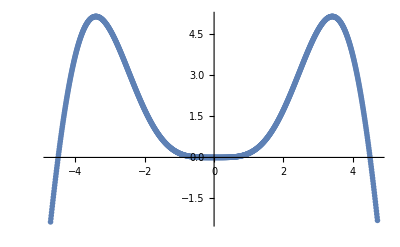

```mathematica
g1 =ListPlot[datosEmpaquetados,PlotStyle->PointSize[0.01]]
```

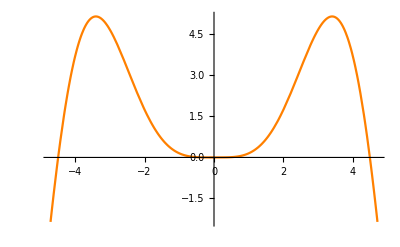

```mathematica
g2 =Plot[1/2 t Sin[t] - t^2/2 Cos[t],{t,-1.5Pi,1.5Pi},PlotStyle->Orange]
```

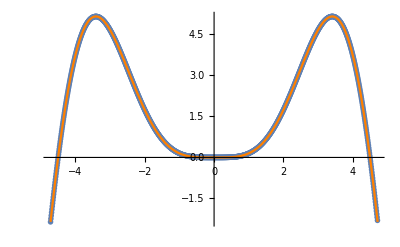

```mathematica
Show[g1,g2]
```

```mathematica
(*Superponiendo  obtenida numericamente es la misma que la obtenida analitica*)
```